```mathematica
patm=98000; (* Pascals *)
Tamb=293; (* Kelvin *)
(* nR=800e-8 (* n (moles)*R (cte gases) *) *)
NN=6 10^15 ;(* Num Particulas *)
kb=1.38 10^-23 ;(* J/K *)

ρ=1000 ;(* kg/m^3 *)
μ=0.001 ;(* Pa*s==kg/s *)
σ=7 10^-2  ;(* N/m *)

Ps[t_,A_,ω_,δ_]:= A Sin[t ω + δ]

A=2patm;
ω=2π*1000;
δ=π/2;
```

{{R→InterpolatingFunction[…],T→InterpolatingFunction[…]}}

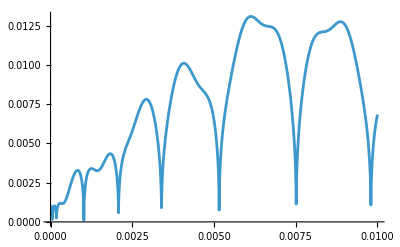

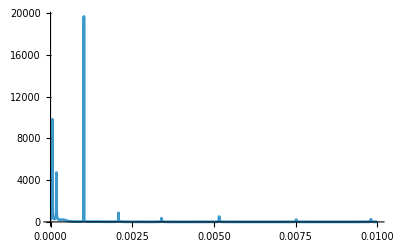

```mathematica
Clear[s]
s =NDSolve[{
R''[t]==1/R[t](-(3 (R'[t])^2)/2+1/ρ((3 NN kb T[t])/(4 π (R[t])^3)-(2 σ + 4μ R'[t])/R[t]-patm-Ps[t,A,ω,δ])),
T'[t]==-(2T[t]R'[t])/R[t],
R'[0]==0,R[0]==10^-3,T[0]==Tamb},
{R,T},{t,0,0.01},
MaxStepSize->0.0001, Method->{"TimeIntegration"->{"ExplicitRungeKutta","DifferenceOrder"->6}},MaxSteps->10^6]
Plot[R[t]/.s,{t,0,0.01}]
Plot[T[t]/.s,{t,0,0.01},PlotRange->All]
```